## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/snake/";  
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/mercury/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.378661 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.1.0 for Mac OS X x86

date: May 11, 2020, time: 03:15:13

nb: /Users/dantopa/Mathematica_files/nb/ert/mercury/snake/probability density function.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.378661 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,3},{Automatic,Automatic}};
```

```mathematica
isize=ImageSize->5 72;
```

#### functions

#### substitutions

#### modules

## 1

https : // en.wikipedia.org/wiki/Normal_distribution

```mathematica
Clear[f];
f[x_,μ_,σ_]:=1/(σ √(2π))Exp[-1/2((x-μ)/σ)^2]
```

```mathematica
μ=1;
σ=1;
λ=3;
hi:=μ+λ σ;
lo:=μ-λ σ;
g001=Plot[f[x,μ,σ],{x,lo,hi},
PlotStyle->Black,
Filling->Axis,
FillingStyle->{Blue,Opacity[0.1]},
Frame->True,
Axes->False];
```

```mathematica
μ=3;
σ=0.15;
λ=3;
g002=Plot[f[x,μ,σ],{x,lo,hi},
PlotStyle->Black,
Filling->Axis,
FillingStyle->{Gray,Opacity[0.1]},
Frame->True,
Axes->False]
```

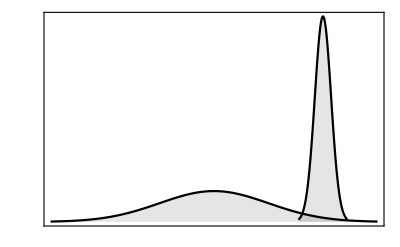

```mathematica
g=Show[{g001,g002},
ImagePadding->{{3,3},{3,3}},
FrameTicks->{{None,Automatic},{None,Automatic}},
PlotRange->Full]
```

```mathematica
multiExport["probability-density",g]
```

## 2

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```